## 图示

```mathematica
Clear["Global`*"]
```

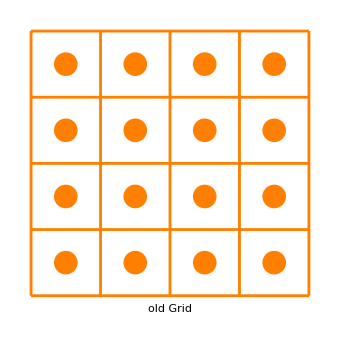

```mathematica
nPoint1=4;delta1=2/nPoint1;
Graphics[{
{Thickness[0.006],RGBColor[1,0.5,0],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]
]},
Text[Style["old Grid",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

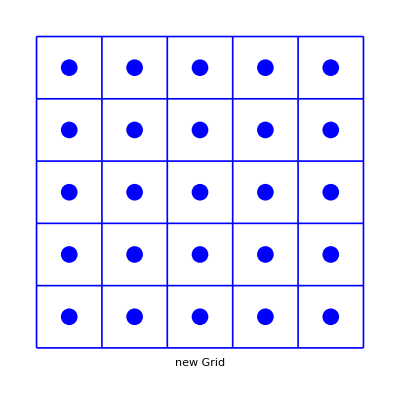

```mathematica
nPoint2=5;delta2=2/nPoint2;
Graphics[{
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}]
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["new Grid",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

### Align = True (TensorFlow, mxnet, pyTorch, TensorRT)

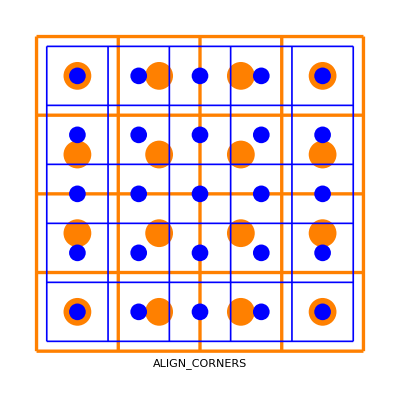

```mathematica
Graphics[{
{Thickness[0.006],RGBColor[1,0.5,0],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]*(1-1/nPoint2)/(1-1/nPoint1)(*adjusted old Grid*)
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]*(1-1/nPoint2)/(1-1/nPoint1)
]},
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}](*unchanged new Grid*)
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["ALIGN_CORNERS",Large],{0,-1.15}]
},AspectRatio->1,PlotRange->1.25,Axes->False,Frame->False]
```

### Align = False (TensorFlow, mxnet, TensorRT<7, OpenCV[warpAffine])

```mathematica
δ=1/nPoint2-1/nPoint1;
Graphics[{
{Thickness[0.005],RGBColor[1,0.5,0],Line[
Map[#+{{δ,-δ},{δ,-δ}}&,
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]
]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i+δ,j-δ},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]
]},
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}](*unchanged new Grid*)
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["ASYMMETRIC,step1",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

-Graphics-

```mathematica
fixPoint2X[x_]:=Min[x,1-1/nPoint1+δ];
fixPoint2Y[x_]:=Max[x,-1+1/nPoint1-δ];
δ=1/nPoint2-1/nPoint1;
Graphics[{
{Thickness[0.005],RGBColor[1,0.5,0],Line[
Map[#+{{δ,-δ},{δ,-δ}}&,
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]
]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i+δ,j-δ},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]
]},
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}](*unchanged new Grid*)
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{fixPoint2X[i],fixPoint2Y[j]},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["ASYMMETRIC,step2",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

-Graphics-

### Align = False (pyTorch, TensorRT≥7, OpenCV[resize]), two steps

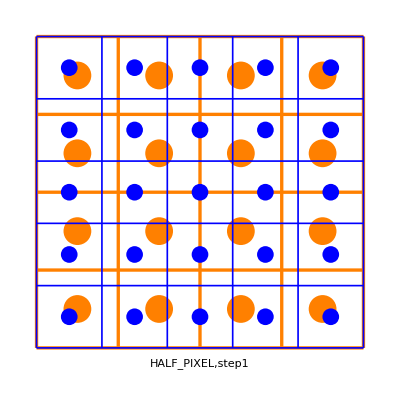

```mathematica
Graphics[{
{Thickness[0.006],RGBColor[1,0.5,0],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]
]},
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}](*unchanged new Grid*)
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["HALF_PIXEL,step1",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```

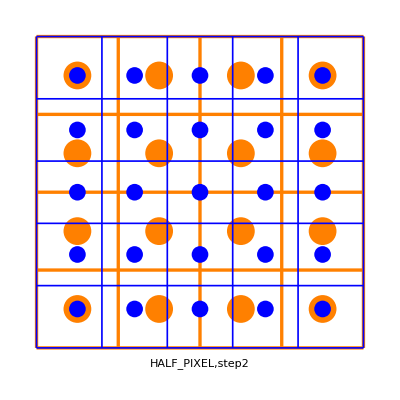

```mathematica
fixPoint2[x_]:=Min[Max[x,-1+1/nPoint1],1-1/nPoint1];
Graphics[{
{Thickness[0.006],RGBColor[1,0.5,0],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta1}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta1}]
]},
{PointSize[0.05],RGBColor[1,0.5,0],Point[
Flatten[Table[{i,j},{i,-1+1/nPoint1,1-1/nPoint1,delta1},{j,-1+1/nPoint1,1-1/nPoint1,delta1}],1]
]},
{Thickness[0.003],RGBColor[0,0,1],Line[
Table[{{i,-1},{i,1}},{i,-1,1,delta2}]~Join~Table[{{-1,i},{1,i}},{i,-1,1,delta2}](*unchanged new Grid*)
]},
{PointSize[0.03],RGBColor[0,0,1],Point[
Flatten[Table[{fixPoint2[i],fixPoint2[j]},{i,-1+1/nPoint2,1-1/nPoint2,delta2},{j,-1+1/nPoint2,1-1/nPoint2,delta2}],1]
]},
Text[Style["HALF_PIXEL,step2",Large],{0,-1.1}]
},AspectRatio->1,PlotRange->1.2,Axes->False,Frame->False]
```